```mathematica
FR$Parallel=False;
$FeynRulesPath=SetDirectory["/home/yoxara/feynrules-current"];
<<FeynRules`
SetDirectory[NotebookDirectory[]];
LoadModel["/home/yoxara/2MDM/models/Feynrules/2MDM/2MDMnlo.fr"];
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

Yoxara Villamizar

Model Version: 1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model 2MDMnlo loaded.

```mathematica
(*CheckHermiticity[L2MDM,FlavorExpand->True]*)
```

```mathematica
vertices=FeynmanRules[L2MDM];(*,Exclude4Scalars->True*)
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

152 possible non-zero vertices have been found -> starting the computation:  / 152.

147 vertices obtained.

```mathematica
(*FeynmanRules[L2MDM,FlavorExpand->True]*)
```

```mathematica
decays=Simplify[ComputeWidths[vertices]];
```

Flavor expansion of the vertices:  / 147

Computing the squared matrix elements relevant for the 1->2 decays:

/ 72

```mathematica
(*Simplify[TotWidth[Zp,decays]]*)
```

```mathematica
(*WriteLaTeXOutput[L2MDM,Output]*)
```

```mathematica
(*Decay_Zp*)
gqA = 0;
Zpuu =  FullSimplify[Collect[PartialWidth[{Zp, u, ubar},decays]/. MU^2->x*MZp^2,x,Simplify]]/. x->MU^2/MZp^2
Zpcc = FullSimplify[Collect[PartialWidth[{Zp, c, cbar},decays]/. MC^2->x*MZp^2,x,Simplify]]/. x->MC^2/MZp^2
Zptt =  FullSimplify[Collect[PartialWidth[{Zp, t, tbar},decays]/. MT^2->x*MZp^2,x,Simplify]]/. x->MT^2/MZp^2
Zpdd = FullSimplify[Collect[PartialWidth[{Zp, d, dbar},decays]/. MD^2->x*MZp^2,x,Simplify]]/. x->MD^2/MZp^2
Zpss = FullSimplify[Collect[PartialWidth[{Zp, s, sbar},decays]/. MS^2->x*MZp^2,x,Simplify]]/. x->MS^2/MZp^2
Zpbb = FullSimplify[Collect[PartialWidth[{Zp, b, bbar},decays]/. MB^2->x*MZp^2,x,Simplify]]/. x->MB^2/MZp^2
Zpdmdm =  FullSimplify[Collect[PartialWidth[{Zp, chibar, chibar},decays]/. MchiT^2->x*MZp^2,x,Simplify]]/. x->MchiT^2/MZp^2
```

(g_Zp^2 (g_qL^2+g_qA^2-((g_qL^2-6 g_qL g_qA+g_qA^2) MU^2)/MZp^2) MZp^2 √((1-(4 MU^2)/MZp^2) MZp^4))/(8 π Abs[MZp]^3)

(g_Zp^2 (g_qL^2+g_qA^2-((g_qL^2-6 g_qL g_qA+g_qA^2) MC^2)/MZp^2) MZp^2 √((1-(4 MC^2)/MZp^2) MZp^4))/(8 π Abs[MZp]^3)

(g_Zp^2 (g_qL^2+g_qA^2-((g_qL^2-6 g_qL g_qA+g_qA^2) MT^2)/MZp^2) MZp^2 √((1-(4 MT^2)/MZp^2) MZp^4))/(8 π Abs[MZp]^3)

(g_Zp^2 (g_qL^2+g_qA^2-((g_qL^2-6 g_qL g_qA+g_qA^2) MD^2)/MZp^2) MZp^2 √((1-(4 MD^2)/MZp^2) MZp^4))/(8 π Abs[MZp]^3)

(g_Zp^2 (g_qL^2+g_qA^2-((g_qL^2-6 g_qL g_qA+g_qA^2) MS^2)/MZp^2) MZp^2 √((1-(4 MS^2)/MZp^2) MZp^4))/(8 π Abs[MZp]^3)

(g_Zp^2 (g_qL^2+g_qA^2-((g_qL^2-6 g_qL g_qA+g_qA^2) MB^2)/MZp^2) MZp^2 √((1-(4 MB^2)/MZp^2) MZp^4))/(8 π Abs[MZp]^3)

(g_chi^2 (-4 Mchi^2+MZp^2) √(-4 Mchi^2 MZp^2+MZp^4))/(24 π Abs[MZp]^3)

```mathematica
MZp = 250;
496.051*BranchingRatio[{Zp, chibar, chibar},decays]
```

44.5634

```mathematica
sduu = FullSimplify[Collect[PartialWidth[{sd, u, ubar},decays]/. MU^2->x*MSd^2,x,Simplify]]/. x->MU^2/MSd^2
StringReplace[ToString[sduu,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sddd= FullSimplify[Collect[ PartialWidth[{sd, d, dbar},decays]/. MD^2->x*MSd^2,x,Simplify]]/. x->MD^2/MSd^2
StringReplace[ToString[sddd,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdcc =   FullSimplify[Collect[PartialWidth[{sd, c, cbar},decays]/. MC^2->x*MSd^2,x,Simplify]]/. x->MC^2/MSd^2
StringReplace[ToString[sdcc,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdss=  FullSimplify[Collect[PartialWidth[{sd, s, sbar},decays]/. MS^2->x*MSd^2,x,Simplify]]/. x->MS^2/MSd^2
StringReplace[ToString[sdss,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdtt =FullSimplify[Collect[ PartialWidth[{sd, t, tbar},decays]/. MT^2->x*MSd^2,x,Simplify]]/. x->MT^2/MSd^2
StringReplace[ToString[sdtt,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdbb  =FullSimplify[Collect[ PartialWidth[{sd, b, bbar},decays]/. MB^2->x*MSd^2,x,Simplify]]/. x->MB^2/MSd^2
StringReplace[ToString[sdbb,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sddmdm =FullSimplify[Collect[PartialWidth[{sd, chibar, chibar},decays]/. Mchi^2->x*MSd^2,x,Simplify]]/. x->Mchi^2/MSd^2
StringReplace[ToString[sddmdm,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdee = FullSimplify[Collect[PartialWidth[{sd,e,ebar},decays]/. Me^2->x*MSd^2,x,Simplify]]/. x->Me^2/MSd^2
StringReplace[ToString[sdee,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdmumu = FullSimplify[Collect[PartialWidth[{sd,mu, mubar},decays]/. MMU^2->x*MSd^2,x,Simplify]]/. x->MMU^2/MSd^2
StringReplace[ToString[sdmumu,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdtata=FullSimplify[Collect[ PartialWidth[{sd, ta, tabar},decays]/. MTA^2->x*MSd^2,x,Simplify]]/. x->MTA^2/MSd^2
StringReplace[ToString[sdtata,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdhh =FullSimplify[Collect[PartialWidth[{sd,h,h},decays] /. Mh^2->x*MSd^2,x,Simplify]]/. x->Mh^2/MSd^2
StringReplace[ToString[sdhh,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
ee=(2*MW*sw)/vev
sdZZ = FullSimplify[Collect[ PartialWidth[{sd, Z, Z},decays]/. MZ^2->x*MSd^2,x,Simplify]]/. x->MZ^2/MSd^2
StringReplace[ToString[sdZZ,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
sdWW =FullSimplify[Collect[  PartialWidth[{sd,Wbar, W},decays] /. MW^2->x*MSd^2,x,Simplify]]/. x->MW^2/MSd^2
StringReplace[ToString[sdWW,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
(*sdZpZp=FullSimplify[Collect[(Subscript[c, α]^2 Subscript[g, sd]^4 Subscript[g, Zp]^4 √(Subscript[M, s]^4-4 Subscript[M, s]^2 MZp^2) (Subscript[M, s]^4-4 Subscript[M, s]^2 MZp^2+12 MZp^4) Subscript[υ, s]^2)/(32 MZp^4 π Abs[Subscript[M, s]]^3)/. MZp^2->x*Subscript[M, s]^2,x,Simplify]]/. x->MZp^2/Subscript[M, s]^2*)
```

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

(2 M_W s_w)/vev

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Null

```mathematica
(*lam1=MH1^2/(2*vev^2)*Ca^2+MSd^2/(2*vev^2)*Sa^2;
lam2=MH1^2/(2*xev^2)*Sa^2+MSd^2/(2*xev^2)*Ca^2;
lam3=(MSd^2-MH1^2)/(xev*vev)*Sa*Ca;*)
Ca = Cos[θ];
Sa = Sin[θ];
gchi = MZp/(2*xev)
lam1=(MH1^2+MSd^2+(MH1^2-MSd^2)*(Ca^2-Sa^2))/(4*vev^2)
lam2=(gchi^2*(MH1^2+MSd^2+(-MH1^2+MSd^2)*(Ca^2-Sa^2)))/MZp^2
lam3=(2*Ca*gchi*(MH1^2-MSd^2)*Sa)/(MZp*vev)
```

MZp/(2 xev)

```mathematica
(MH1^2+MSd^2+(MH1^2-MSd^2) (Cos[θ]^2-Sin[θ]^2))/(4 vev^2)
```

```mathematica
(MH1^2+MSd^2+(-MH1^2+MSd^2) (Cos[θ]^2-Sin[θ]^2))/(4 xev^2)
```

```mathematica
((MH1^2-MSd^2) Cos[θ] Sin[θ])/(vev xev)
```

```mathematica
PartialWidth[{sd,H1,H1},decays]
```

```mathematica
1/(128 π vev^2 xev^2 Abs[MSd]^3)√(MSd^2 (-4 MH1^2+MSd^2)) Cos[θ]^2 Sin[θ]^2 (3 MH1^2 xev Cos[θ]+3 MSd^2 xev Cos[θ]+5 MH1^2 xev Cos[θ]^3-5 MSd^2 xev Cos[θ]^3+3 MH1^2 vev Sin[θ]+3 MSd^2 vev Sin[θ]-7 MH1^2 vev Cos[θ]^2 Sin[θ]+7 MSd^2 vev Cos[θ]^2 Sin[θ]-7 MH1^2 xev Cos[θ] Sin[θ]^2+7 MSd^2 xev Cos[θ] Sin[θ]^2+5 MH1^2 vev Sin[θ]^3-5 MSd^2 vev Sin[θ]^3)^2
```

```mathematica
Whh = FullSimplify[Collect[PartialWidth[{sd,H1,H1},decays] /. MH1^2->x*MSd^2,x,Simplify]]/. x->MH1^2/MSd^2
```

```mathematica
1/(128 π vev^2 xev^2)MSd √((1-(4 MH1^2)/MSd^2) MSd^4) Cos[θ]^2 Sign[MSd]^3 Sin[θ]^2 ((1+(5 MH1^2)/MSd^2) xev Cos[θ]+3 (-1+MH1^2/MSd^2) xev Cos[3 θ]+(1+(5 MH1^2)/MSd^2) vev Sin[θ]-3 (-1+MH1^2/MSd^2) vev Sin[3 θ])^2
```

```mathematica
whsd = FullSimplify[Collect[Whh,-1+MH1^2/MSd^2]]
```

```mathematica
1/(128 (MSd^2)^(3/2) π vev^2 xev^2)√(-4 MH1^2 MSd^2+MSd^4) Cos[θ]^2 Sin[θ]^2 ((5 MH1^2+MSd^2) xev Cos[θ]+3 (MH1-MSd) (MH1+MSd) xev Cos[3 θ]+(5 MH1^2+MSd^2) vev Sin[θ]-3 (MH1-MSd) (MH1+MSd) vev Sin[3 θ])^2
```

```mathematica
FullSimplify[Collect[whsd /. MH1^2->x*MSd^2,x,Simplify]/. x->MH1^2/MSd^2]
```

```mathematica
1/(128 (MSd^2)^(3/2) π vev^2 xev^2)√(-4 MH1^2 MSd^2+MSd^4) Cos[θ]^2 Sin[θ]^2 ((5 MH1^2+MSd^2) xev Cos[θ]+3 (MH1-MSd) (MH1+MSd) xev Cos[3 θ]+(5 MH1^2+MSd^2) vev Sin[θ]-3 (MH1-MSd) (MH1+MSd) vev Sin[3 θ])^2
```

```mathematica
(*Ca = Cos[α];
Sa = Sin[α];
lam1=(1/(4*vev^2))*(MSd^2+MH1^2+(MSd^2-MH1^2)*(2*Ca^2-1));
lam2=(gchi^2/(MZp^2))*(MSd^2+MH1^2+(MH1^2-MSd^2)*(2*Ca^2-1));
lam3=2*qchi*(MSd^2-MH1^2)/(MZp*vev)*Sa*Ca;
mu2h=-lam1*vev^2-lam3/2*xev^2;
mu2sd=-lam3/2*vev^2-lam2*xev^2;
xev=MZp/(2*gchi)
gZp =1*)
(*qchi = MZp/(2*xev)*)
(*MZp 2*xev*qchi*)
```

```mathematica
(*cos[α]^2 sin[α]^2  is 1/4 sin^2[2α]*)
(*lam1=MH1^2/(2*vev^2)*Ca^2+MSd^2/(2*vev^2)*Sa^2;
lam2=MH1^2/(2*xev^2)*Sa^2+MSd^2/(2*xev^2)*Ca^2;
lam3=(MSd^2-MH1^2)/(xev*vev)*Sa*Ca;
mu2H1=-lam1*vev^2-lam3/2*xev^2;
mu2sd=-lam3/2*vev^2-lam2*xev^2;
Ca =cos[α];
Sa =sin[α];Mchi =(1/Sqrt[2])*ychi* xev;*)
```

```mathematica
(*PartialWidth[{sd, Zp, Zp},decays]
PartialWidth[{H1, d, dbar},decays]
PartialWidth[{H1, c, cbar},decays]
PartialWidth[{H1, s, sbar},decays]
PartialWidth[{H1, t, tbar},decays]
PartialWidth[{H1, b, bbar},decays]
PartialWidth[{H1, chi, chibar},decays]
BranchingRatio[{sd,chi,chibar},decays]
BranchingRatio[{Zp,chi,chibar},decays]*)
```

```mathematica
(*WriteLaTeXOutput[L2MDM,Output]*)
```

```mathematica
(*Expand[L2MDM];*)
```

```mathematica
Ca = Cos[θ];
Sa = Sin[θ];
lam1=(MH1^2+MSd^2+(MH1^2-MSd^2)*(Ca^2-Sa^2))/(4*vev^2);
lam2=(gchi^2*(MH1^2+MSd^2+(-MH1^2+MSd^2)*(Ca^2-Sa^2)))/MZp^2;
lam3=(2*Ca*gchi*(MH1^2-MSd^2)*Sa)/(MZp*vev);
Simplify[(2 Ca^2 (3 lam1-lam3) Sa vev+lam3 Sa^3 vev+Ca^3 lam3 xev+2 Ca (3 lam2-lam3) Sa^2 xev)]
```

```mathematica
1/(8 MZp^2 vev)(MZp (MSd^2 (3 MZp-2 gchi xev)+MH1^2 (9 MZp+2 gchi xev)) Cos[θ]+3 (MH1^2-MSd^2) MZp (MZp+2 gchi xev) Cos[3 θ]-4 gchi vev (MH1^2 (MZp-6 gchi xev)-MSd^2 (MZp+6 gchi xev)+3 (MH1^2-MSd^2) (MZp+2 gchi xev) Cos[2 θ]) Sin[θ]) Sin[2 θ]
```

```mathematica
FullSimplify[1/(8 MZp^2 vev)(MZp (MSd^2 (3 MZp-MZp)+MH1^2 (9 MZp+MZp)) Cos[θ]+3 (MH1^2-MSd^2) MZp (MZp+MZp) Cos[3 θ]-4 Subscript[g, chi] vev (MH1^2 (MZp-3MZp)-MSd^2 (MZp+3MZp)+3 (MH1^2-MSd^2) (MZp+MZp) Cos[2 θ]) Sin[θ]) Sin[2 θ]]
```

```mathematica
1/(2 MZp vev)Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MSd^2+3 (MH1-MSd) (MH1+MSd) Cos[2 θ])+vev ((5 MH1^2+MSd^2) Sin[θ]+3 (-MH1^2+MSd^2) Sin[3 θ]) Subscript[g, chi])
```

```mathematica
3 (MH1-MSd) (MH1+MSd)
```

```mathematica
3 (MH1-MSd) (MH1+MSd)
```

```mathematica
Expand[3 (MH1-MSd) (MH1+MSd)]
```

```mathematica
3 MH1^2-3 MSd^2
```

```mathematica
1/(2 MZp vev)Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MSd^2+(3 MH1^2-3 MSd^2) Cos[2 θ])+vev ((5 MH1^2+MSd^2) Sin[θ]+3 (-MH1^2+MSd^2) Sin[3 θ]) Subscript[g, chi])
```

```mathematica
1/(2 MZp vev)Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MSd^2+(3 MH1^2-3 MSd^2) Cos[2 θ])+vev ((5 MH1^2+MSd^2) Sin[θ]+3 (-MH1^2+MSd^2) Sin[3 θ]) Subscript[g, chi])
```

```mathematica
FullSimplify[1/(2 MZp vev)Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MSd^2+(3 MH1^2-3 MSd^2) Cos[2 θ])+vev ((5 MH1^2+MSd^2) Sin[θ]+3 (-MH1^2+MSd^2) Sin[3 θ]) Subscript[g, chi])]
```

```mathematica
FullSimplify[Collect[1/(2 MZp vev)Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MSd^2+(3 MH1^2-3 MSd^2) Cos[2 θ])+vev ((5 MH1^2+MSd^2) Sin[θ]+3 (-MH1^2+MSd^2) Sin[3 θ]) Subscript[g, chi])/. MH1^2->x*MSd^2,x,Simplify]]/. x->MH1^2/MSd^2
```

```mathematica
(MSd^2 Sin[2 θ] (MZp Cos[θ] (2+MH1^2/MSd^2+3 (-1+MH1^2/MSd^2) Cos[2 θ])+2 vev (2+MH1^2/MSd^2-3 (-1+MH1^2/MSd^2) Cos[2 θ]) Sin[θ] Subscript[g, chi]))/(2 MZp vev)
```

```mathematica
(MSd^2 Sin[2 θ] (MZp Cos[θ] (2+z^2+3 (-1+z^2) Cos[2 θ])+2 vev (2+z^2-3 (-1+z^2) Cos[2 θ]) Sin[θ] Subscript[g, chi]))/(2 MZp vev)
```

```mathematica
Ca = Sqrt[1-Sa^2];
FullSimplify[Collect[(MSd^2 (2Sa Ca) (MZp Ca (2+z^2+3 (-1+z^2) (1-2 Sa^2))+2 vev (2+z^2-3 (-1+z^2)  (1-2 Sa^2))Sa Subscript[g, chi]))/(2 MZp vev),Sa]]
```

```mathematica
(MSd^2 Sa (MZp (-1+Sa^2) (1-4 z^2+6 Sa^2 (-1+z^2))+2 Sa √(1-Sa^2) vev (5-2 z^2+6 Sa^2 (-1+z^2)) Subscript[g, chi]))/(MZp vev)
```

```mathematica
(MSd^2 Sa (MZp (-Ca^2) (1-4 z^2+6 Sa^2 (-1+z^2))+2 Sa Ca vev (5-2 z^2+6 Sa^2 (-1+z^2)) Subscript[g, chi]))/(MZp vev)
```

```mathematica
(MSd^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca Sa vev (5-2 z^2+6 Sa^2 (-1+z^2)) Subscript[g, chi]))/(MZp vev)
```

```mathematica
Simplify[(MSd^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca Sa vev (5-2 z^2+6 Sa^2 (-1+z^2)) Subscript[g, chi]))/(MZp vev)]
```

```mathematica
(MSd^2 Sin[2 θ] (2 MZp Cos[θ] (2+z^2+3 (-1+z^2) Cos[2 θ])-4 vev (-2-z^2+3 (-1+z^2) Cos[2 θ]) Sin[θ] Subscript[g, chi]))/(4 MZp vev)
```

```mathematica
shh = (((√(1-4 z^2))/(32 π MSd))[(MSd^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca Sa vev (5-2 z^2+6 Sa^2 (-1+z^2)) gchi))/(MZp vev)])^2
```

```mathematica
(((√(1-4 z^2))/(32 MSd π))[(MSd^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca gchi Sa vev (5-2 z^2+6 Sa^2 (-1+z^2))))/(MZp vev)])^2
```

```mathematica
StringReplace[ToString[shh,InputForm],{"Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
```

```mathematica
"(sy.sqrt(1 - 4*z**2)/(32*MSd*sy.pi))((MSd**2*Sa*(-(Ca**2*MZp*(1 - 4*z**2 + 6*Sa**2*(-1 + z**2))) + 2*Ca*gchi*Sa*vev*(5 - 2*z**2 + 6*Sa**2*(-1 + z**2))))/(MZp*vev))**2"
```

```mathematica
lam1=(MH1^2+MSd^2+(MH1^2-MSd^2)*(Ca^2-Sa^2))/(4*vev^2);
lam2=(gchi^2*(MH1^2+MSd^2+(-MH1^2+MSd^2)*(Ca^2-Sa^2)))/MZp^2;
lam3=(2*Ca*gchi*(MH1^2-MSd^2)*Sa)/(MZp*vev);
```

```mathematica
NF= Sqrt[1-4 MH1^2/MSd^2]/(32 π MSd)
```

```mathematica
(√(1-(4 MH1^2)/MSd^2))/(32 MSd π)
```

```mathematica
GammaShh = NF*R
```

```mathematica
(√(1-(4 MH1^2)/MSd^2) R)/(32 MSd π)
```

```mathematica
Ca = Cos[θ];
Sa = Sin[θ];
```

```mathematica
MZp = 2 gchi xev;
Fa = FullSimplify[ (2 Ca^2 (3 lam1-lam3) Sa vev+lam3 Sa^3 vev+Ca^3 lam3 xev+2 Ca (3 lam2-lam3) Sa^2 xev)^2]
```

```mathematica
1/(16 vev^2 xev^2)Sin[2 θ]^2 ((5 MH1^2+MSd^2) xev Cos[θ]+3 (MH1-MSd) (MH1+MSd) xev Cos[3 θ]+(5 MH1^2+MSd^2) vev Sin[θ]-3 (MH1-MSd) (MH1+MSd) vev Sin[3 θ])^2
```

```mathematica
Fa = 1/(16 vev^2 xev^2)Sin[2 θ]^2 ((5 MH1^2+MSd^2) xev Cos[θ]+3 (MH1^2-MSd^2) xev Cos[3 θ]+(5 MH1^2+MSd^2) vev Sin[θ]-3 (MH1^2-MSd^2) vev Sin[3 θ])^2
```

```mathematica
1/(16 vev^2 xev^2)Sin[2 θ]^2 ((5 MH1^2+MSd^2) xev Cos[θ]+3 (MH1^2-MSd^2) xev Cos[3 θ]+(5 MH1^2+MSd^2) vev Sin[θ]-3 (MH1^2-MSd^2) vev Sin[3 θ])^2
```

```mathematica
Fa2 = FullSimplify[Collect[ Fa/. MH1^2->x*MSd^2,x,Simplify]]/. x->MH1^2/MSd^2
```

```mathematica
(MSd^4 Sin[2 θ]^2 ((1+(5 MH1^2)/MSd^2) xev Cos[θ]+3 (-1+MH1^2/MSd^2) xev Cos[3 θ]+(1+(5 MH1^2)/MSd^2) vev Sin[θ]-3 (-1+MH1^2/MSd^2) vev Sin[3 θ])^2)/(16 vev^2 xev^2)
```

```mathematica
R=  FullSimplify[Collect[ Fa2 /. MH1^2->z*MSd^2,z,Simplify]]
```

```mathematica
(MSd^4 Sin[2 θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(16 vev^2 xev^2)
```

```mathematica
xev = MZp/(2 gchi);
```

```mathematica
R = FullSimplify[Collect[R,Sin[θ]]]
```

```mathematica
(MSd^4 Sin[2 θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(16 vev^2 xev^2)
```

```mathematica
NF= Sqrt[1-4 MH1^2/MSd^2]/(32 π MSd);
R= 1/(4 vev^2 xev^2)Ca^2 MSd^4 Sa^2 (-7 Ca^2 Sa vev (-1+z)+5 Sa^3 vev (-1+z)+5 Ca^3 xev (-1+z)-7 Ca Sa^2 xev (-1+z)+3 Sa vev (1+z)+3 Ca xev (1+z))^2;

GammaShh = FullSimplify[ NF*R]
```

```mathematica
1/(128 π vev^2 xev^2)√(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Sin[θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2
```

```mathematica
StringReplace[ToString[GammaShh,InputForm],{"Abs"->"abs","Sin"-> "sin","Cos"->"cos","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi","θ"->"theta"}]
```

```mathematica
"(sy.sqrt(1 - (4*MH1**2)/MSd**2)*MSd**3*cos(theta)**2*sin(theta)**2*(xev*(1 + 5*z)*cos(theta) + 3*xev*(-1 + z)*cos(3*theta) + vev*(1 + 5*z)*sin(theta) - 3*vev*(-1 + z)*sin(3*theta))**2)/(128*sy.pi*vev**2*xev**2)"
```

```mathematica
TeXForm[GammaShh]
```

```mathematica
\frac{\text{MSd}^3 \sin^2(\theta ) \cos^2(\theta ) \sqrt{1-\frac{4 \text{MH1}^2}{\text{MSd}^2}} (\text{vev} (5 z+1) \sin (\theta )-3 \text{vev} (z-1) \sin (3 \theta )+\text{xev} (5 z+1) \cos (\theta )+3 \text{xev} (z-1) \cos (3
   \theta ))^2}{128 \pi v^2 v_s^2}
```

```mathematica
z = MH1^2/MSd^2;
```

```mathematica
FullSimplify[((5z+1)/(z-1))]
```

5+6/(-1+z)

```mathematica
Denominator[(1+5 z)/(-1+z)]
```

-1+z

```mathematica
FullSimplify[((z-1)/(5z+1))((z-1)/(z-1))]
```

(-1+z)/(1+5 z)

```mathematica
Expand[1/(128 π vev^2 xev^2)√(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Sin[θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2]
```

```mathematica
(√(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^4 Sin[θ]^2)/(128 π vev^2)+(5 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^4 Sin[θ]^2)/(64 π vev^2)+(25 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^4 Sin[θ]^2)/(128 π vev^2)-(3 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^3 Cos[3 θ] Sin[θ]^2)/(64 π vev^2)-(3 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^3 Cos[3 θ] Sin[θ]^2)/(16 π vev^2)+(15 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^3 Cos[3 θ] Sin[θ]^2)/(64 π vev^2)+(9 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Cos[3 θ]^2 Sin[θ]^2)/(128 π vev^2)-(9 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^2 Cos[3 θ]^2 Sin[θ]^2)/(64 π vev^2)+(9 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^2 Cos[3 θ]^2 Sin[θ]^2)/(128 π vev^2)+(√(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^3 Sin[θ]^3)/(64 π vev xev)+(5 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^3 Sin[θ]^3)/(32 π vev xev)+(25 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^3 Sin[θ]^3)/(64 π vev xev)-(3 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Cos[3 θ] Sin[θ]^3)/(64 π vev xev)-(3 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^2 Cos[3 θ] Sin[θ]^3)/(16 π vev xev)+(15 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^2 Cos[3 θ] Sin[θ]^3)/(64 π vev xev)+(√(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Sin[θ]^4)/(128 π xev^2)+(5 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^2 Sin[θ]^4)/(64 π xev^2)+(25 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^2 Sin[θ]^4)/(128 π xev^2)+(3 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^3 Sin[θ]^2 Sin[3 θ])/(64 π vev xev)+(3 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^3 Sin[θ]^2 Sin[3 θ])/(16 π vev xev)-(15 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^3 Sin[θ]^2 Sin[3 θ])/(64 π vev xev)-(9 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[3 θ])/(64 π vev xev)+(9 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[3 θ])/(32 π vev xev)-(9 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[3 θ])/(64 π vev xev)+(3 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Sin[θ]^3 Sin[3 θ])/(64 π xev^2)+(3 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^2 Sin[θ]^3 Sin[3 θ])/(16 π xev^2)-(15 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^2 Sin[θ]^3 Sin[3 θ])/(64 π xev^2)+(9 √(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Sin[θ]^2 Sin[3 θ]^2)/(128 π xev^2)-(9 √(1-(4 MH1^2)/MSd^2) MSd^3 z Cos[θ]^2 Sin[θ]^2 Sin[3 θ]^2)/(64 π xev^2)+(9 √(1-(4 MH1^2)/MSd^2) MSd^3 z^2 Cos[θ]^2 Sin[θ]^2 Sin[3 θ]^2)/(128 π xev^2)
```

```mathematica
Simplify[%40]
```

```mathematica
1/(128 π vev^2 xev^2)√(1-(4 MH1^2)/MSd^2) MSd^3 Cos[θ]^2 Sin[θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2
```

```mathematica
mh=125;
v=246.158;
gchi=1;
mZp=5000;
theta=0.5;
(-mh^2*Cos[theta]^2+8*Pi*v^2)/Sin[theta]^2
(-gchi^2*mh^2*Sin[theta]^2+2*Pi*mZp^2)/(gchi^2*Cos[theta]^2)
mh^2-4*Pi*mZp*v/(gchi*Sin[2*theta])
```

6.57325×10^6

2.03955×10^8

-1.83648×10^7

```mathematica
125^2
```

15625

```mathematica
4*Pi*100*v/(gchi*Sin[2*theta])
```

735216.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

GreaterEqual::nord: Invalid comparison with ComplexInfinity attempted.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Filling::invfillentry: {Indeterminate} is not a valid Filling specification.

GreaterEqual::nord: Invalid comparison with ComplexInfinity attempted.

Filling::invfillentry: {Indeterminate} is not a valid Filling specification.

General::stop: Further output of Filling::invfillentry will be suppressed during this calculation.

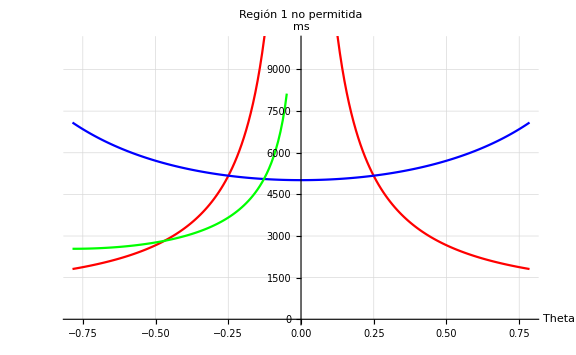

```mathematica
(*Definición de constantes*)mh=125;
v=256;
gchi=0.5;
mZp=1000;

(*Rango de valores para theta*)
thetaValues=Range[-Pi/4,Pi/4,Pi/400];

(*Resolver las desigualdades para cada valor de theta*)
msInvalidValues1=Table[Sqrt[(-1.0*mh^2*Cos[theta]^2+8*Pi*v^2)/Sin[theta]^2],{theta,thetaValues}];
msInvalidValues2=Table[Sqrt[(-gchi^2*mh^2*Sin[theta]^2+2*Pi*mZp^2)/(gchi^2*Cos[theta]^2)],{theta,thetaValues}];
msInvalidValues3=Table[If[(mh^2-4*Pi*mZp*v/(gchi*Sin[2*theta]))>=0,Sqrt[mh^2-4*Pi*mZp*v/(gchi*Sin[2*theta])],Indeterminate],{theta,thetaValues}];

(*Plotting*)
upperLimit=1.5*Max[Max[msInvalidValues1],Max[msInvalidValues2],Max[msInvalidValues3]];

Show[ListLinePlot[{thetaValues,msInvalidValues1}//Transpose,Filling->{1->{upperLimit}},FillingStyle->Directive[Opacity[0.3],Red],PlotStyle->Red,PlotLabel->"Región 1 no permitida"],ListLinePlot[{thetaValues,msInvalidValues2}//Transpose,Filling->{1->{upperLimit}},FillingStyle->Directive[Opacity[0.3],Blue],PlotStyle->Blue,PlotLabel->"Región 2 no permitida"],ListLinePlot[{thetaValues,msInvalidValues3}//Transpose,Filling->{1->{upperLimit}},FillingStyle->Directive[Opacity[0.3],Green],PlotStyle->Green,PlotLabel->"Región 3 no permitida"],PlotRange->{{-Pi/4,Pi/4},{0,10000}},AxesLabel->{"Theta","ms"},GridLines->Automatic,ImageSize->Large]
```